```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
p1=Flatten[Table[{{5-p,5-q,2},{5-p,5-q,1}},{p,1,4},{q,1,4}],2];
p2=Flatten[Table[{{9-p,5-q,2},{9-p,5-q,1}},{p,1,4},{q,1,4}],2];
p3=Flatten[Table[{{4+p,4+q,1},{4+p,4+q,2}},{p,1,4},{q,1,4}],2];
p4=Flatten[Table[{{p,4+q,1},{p,4+q,2}},{p,1,4},{q,1,4}],2];
correspondingNodeCoords=Join[p1,p2,p3,p4];
```

```mathematica
shortenedCoords=Join[p1[[1;;24]],p4[[9;;32]]];
halvedCoords = Join[p1,p4];
shortenedCoordsRightCut=Join[p1[[;;]],p4[[;;24]]];
pFirst = 1;
pLast = 24;
cellInputNode1 = {2,3,"B"};
cellInputNode2 = {3,3,"B"};
```

```mathematica
(*
correspondingNodeCoords: ETI Layer Board Anordnung
shortenedCoords: Nur 48 relevante Nodes
*)
```

```mathematica
measurementDirs//Dimensions
```

{}

```mathematica
files//Dimensions
```

{}

```mathematica
dirs//Dimensions
```

{}

```mathematica
files//Dimensions
```

{}

```mathematica
path="C:\\Users\\Nelson's Laptop\\Documents\\Git\\eti\\Data\\Dynamic_Mesasurements\\2022_09_15\\Edited data\\";
(*measurementDirs=FileNames["*_Data",path];*)
(*path="C:\\Users\\Nelson's Laptop\\Documents\\Git\\eti\\Data\\Dynamic_Mesasurements\\2022_05_23\\";*)
measurementDirs=FileNames["*_90degrees",path];
dirs=FileNames["*",#]&/@measurementDirs;
files=Map[FileNames[#<>"\\*.txt"]&,dirs,{-1}];
tbltmp=Flatten[#,1]&/@Map[Import[#,"Table"]&,files,{-1}];
unitOfChannel=tbltmp[[All,All,2]];
tbl=Table[tbltmp[[p,q,r,s]]*If[unitOfChannel[[p,q,s]]=="(mV)",1.*10^-3,1.],{p,1,Dimensions[tbltmp][[1]]},{q,1,Dimensions[tbltmp][[2]]},{r,4,Dimensions[tbltmp[[1,1]]][[1]]},{s,1,Length[tbltmp[[p,q,2]]]}];
```

```mathematica
tbl//Dimensions
```

{2,72,20004,9}

```mathematica
tbl[[1]][[1,All,{1,2}]]//MatrixForm;
```

```mathematica
(*tbl: Sublattice und +- 90° shift, Sektor und J1 bis J2 inputs, Frequenz, (Zeit, 1x ?? Voltage und 7x Oszi. Inputs von J1 to J2)*)
```

```mathematica
dataOfNodes=Map[Flatten[Table[#[[p,All,{1,q}]],{p,1,Dimensions[tbl][[2]]},{q,3,Length[#[[p,1]]]}],1]&,tbl];
```

```mathematica
dataOfNodes//Dimensions
```

{2,504,20004,2}

```mathematica
(*
dataOfNodes: Sublattice und +- 90° shift, P1 Nodes 1-24 und P4 Nodes 9-32 wobei für jede Node die 6 Frequenzen, Zeitverlauf einer Node, (Zeit,Voltages der Node zur Zeit)
*)
```

```mathematica
redtbl = tbl[[;;,;;,;;,3;;]];
correctCoords =shortenedCoordsRightCut;
mergingDataWithCoords=Table[{redtbl[[1,Ceiling[r/7]*8+meas-8,;;,Mod[r,7,1]]],correctCoords[[r]]},{meas,1,Dimensions[files][[3]]},{r,pFirst,32+pLast}];
```

```mathematica
sortedNodes = Table[{x,y,sub},{x,1,Which[pFirst==1,4,pFirst==9,3]},{y,1,8},{sub,1,2}];
sortedNodes//Dimensions
```

{4,8,2,3}

```mathematica
mergingDataWithCoords[[1,1,1]]//Dimensions
```

{20004}

```mathematica
mergingDataWithCoords[[1,Position[mergingDataWithCoords[[1,;;,2]],sortedNodes[[1,1,1]]][[1,1]]]][[2]]//Dimensions
```

{3}

```mathematica
RandomInteger[0,Dimensions[mergingDataWithCoords[[1,1,1]]]];
```

```mathematica
sortedDataWithCorrds = Table[If[Position[mergingDataWithCoords[[1,;;,2]],sortedNodes[[x,y,sub]]]=={},{RandomInteger[0,Dimensions[mergingDataWithCoords[[1,1,1]]]],{x,y,sub}},mergingDataWithCoords[[1,Position[mergingDataWithCoords[[1,;;,2]],sortedNodes[[x,y,sub]]][[1,1]]]]],{x,1,Dimensions[sortedNodes][[1]]},{y,1,Dimensions[sortedNodes][[2]]},{sub,1,Dimensions[sortedNodes][[3]]}];
sortedDataWithCorrds//Dimensions
sortedDataWithCorrds[[1,1,1,1]]//Dimensions
```

{4,8,2,2}

{20004}

```mathematica
sortedDataWithCorrds[[2,1,2,1,;;5]]
```

{-0.0000122085,0.0000427298,0.000094616,0.000094616,0.000149554}

```mathematica
tbl[[1,1,1;;100,1]]//MatrixForm;
```

```mathematica
sortedDataWithCorrds//MatrixForm
```

((1) | ({-0.000252106,-0.000227079,-0.000202051,-0.000239287,-0.000277133,-0.000202051,-0.000227079,-0.000202051,-0.000239287,-0.000289342,-0.000277133,-0.000264315,-0.000264315,19978,-0.000239287,-0.000239287,-0.000239287,-0.000202051,-0.000252106,-0.000239287,-0.000264315,-0.00021426,-0.000239287,-0.000289342,-0.000252106,-0.000252106,-0.000302161} | {1,2,1}
1 | 1) | (1) | ({0.0000900378,0.0000714198,0.00012117,0.0000961421,0.0000463924,0.0000900378,0.0000528018,0.00011476,0.0000961421,0.0000650104,0.0000589061,0.000108656,0.00021426,0.000170919,19976,0.0000961421,0.000133378,0.0000714198,0.0000463924,0.000127274,0.000108656,0.0000836284,0.000152301,0.00012117,0.00011476,0.000145892,0.000133378,0.000127274,0.000177024} | {1,4,1}
{1} | 1) | (1) | ({-0.0000531071,-0.0000158711,-0.0000158711,-0.0000158711,-0.000103162,-3.66256×10^-6,0.0000213649,-3.66256×10^-6,-3.66256×10^-6,-0.0000408985,-0.0000531071,-0.000103162,19980,-0.0000531071,-0.0000408985,-0.00002869,-0.00002869,-0.000065926,-0.0000531071,-3.66256×10^-6,0.0000592113,9.15639×10^-6,-0.00002869,-0.00002869,-0.00002869} | {1,6,1}
{1} | 1) | (1) | ({-3.66256×10^-6,0.0000586009,0.0000463924,0.0000335734,0.0000335734,0.0000463924,0.0000463924,0.0000335734,0.0000586009,9.15639×10^-6,9.15639×10^-6,19982,-0.0000408985,-0.0000280796,-0.0000781345,-0.0000531071,-0.0000781345,-0.0000531071,-0.0000408985,-0.0000158711,9.15639×10^-6,0.0000463924,0.0000213649} | {1,8,1}
{1} | 1)
(1) | (1) | (1) | (1) | (1) | ({-0.00014345,-0.0000366256,-0.000115981,-0.0000900379,-0.0000366256,-0.0000366256,-0.0000625687,0.0000183128,19988,-0.000170919,-0.0000625687,-0.0000625687,-0.000115981,-0.0000625687,-0.000170919,-0.000115981,-0.000170919} | {2,6,1}
{1} | 1) | (1) | (1)
(1) | (1) | (1) | (1) | ({-0.0000335734,-0.0000836284,-0.0000964473,-0.0000714198,-0.0000463924,-0.0000463924,19992,-0.0000714198,-0.0000335734,3.66256×10^-6,-0.0000213649,-0.0000463924,-9.15639×10^-6} | {3,5,1}
{1} | 1) | (1) | ({-0.0000152607,0.0000381516,-0.0000427298,-0.0000152607,0.0000106825,19994,-0.000070199,-0.000149554,-0.0000152607,0.0000915639,-0.000123611} | {3,7,1}
{1} | 1) | (1)
(1) | ({0.000111708,0.000173361,0.00018618,0.00018618,19996,0.000148944,0.000148944,0.000136125,0.000198389} | {4,2,1}
1 | 1) | (1) | ({0.000169698,0.000194726,0.000231962,19998,0.00015749,0.000145281,0.000182517} | {4,4,1}
{1} | 1) | (1) | (1) | (1) | (1))
 |  |  |  |

```mathematica
fitArray//Dimensions
```

{}

```mathematica
fitArray = sortedDataWithCorrds[[;;,;;,;;,1,3002;;3098]];
frequenz=2.28558;
ϕ0=Table[(x-cellInputNode1[[1]])*π/2,{x,1,8}];
omegaRange= 0.995 * 2Pi* frequenz<ω< 1.005 *2 Pi * frequenz;
aBoundaries=Table[Max[fitArray[[x,y,sub]]],{x,1,Dimensions[sortedDataWithCorrds][[1]]},{y,1,Dimensions[sortedDataWithCorrds][[2]]},{sub,1,Dimensions[sortedNodes][[3]]}];
```

```mathematica
aBoundaries[[4,8,1]]
```

0

```mathematica
ϕ0[[2,4]]//MatrixForm
```

Part::partd: Part specification {-π/2,0,π/2,π,(3 π)/2,2 π,(5 π)/2,3 π}⟦2,4⟧ is longer than depth of object.

{-π/2,0,π/2,π,(3 π)/2,2 π,(5 π)/2,3 π}⟦2,4⟧

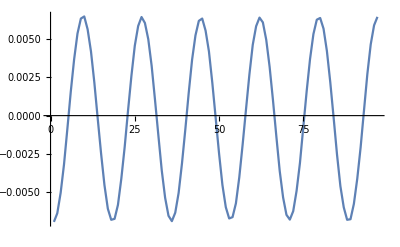

```mathematica
ListLinePlot[sortedDataWithCorrds[[1,1,1,1,2502;;2598]]]
```

```mathematica
fitVars = Table[FindFit[fitArray[[x,y,sub]],{a * Sin[ω * t+ϕ],{If[aBoundaries[[x,y,sub]]==0,0<=a<0.1,0.95*aBoundaries[[x,y,sub]]<=a<1.05*aBoundaries[[x,y,sub]]]0.<ϕ<=2. Pi,omegaRange}},{{a,aBoundaries[[x,y,sub]]},{ω,2Pi* frequenz},{ϕ,ϕ0[[x]]}},t],{x,1,Dimensions[sortedDataWithCorrds][[1]]},{y,1,Dimensions[sortedDataWithCorrds][[2]]},{sub,1,Dimensions[sortedNodes][[3]]}];
```

```mathematica
zeroPhase = ϕ/.fitVars[[cellInputNode1[[1]],cellInputNode1[[2]],If[cellInputNode1[[3]]=="A",1,2],3]];
unitAmp = Max[sortedDataWithCorrds[[cellInputNode1[[1]],cellInputNode1[[2]],If[cellInputNode1[[3]]=="A",1,2],1,2502;;2598]]];

fitFuncsPhases = Table[With[{x=x,y=y,sub=sub},Mod[ω * #+ϕ-zeroPhase,2π]/.fitVars[[x,y,sub,2;;]]&],{x,1,Dimensions[sortedDataWithCorrds][[1]]},{y,1,Dimensions[sortedDataWithCorrds][[2]]},{sub,1,Dimensions[sortedNodes][[3]]}];

fitFuncsAmplitudes = Table[With[{x=x,y=y,sub=sub},Max[sortedDataWithCorrds[[x,y,sub,1,2502;;2598]]]],{x,1,Dimensions[sortedDataWithCorrds][[1]]},{y,1,Dimensions[sortedDataWithCorrds][[2]]},{sub,1,Dimensions[sortedNodes][[3]]}];
```

```mathematica
arrowPlots[t_,sub_]:=Block[{phases = fitFuncsPhases,amplitudes = fitFuncsAmplitudes},
Table[Graphics[Arrow[{{0,0},(amplitudes[[x,y,sub]])/unitAmp*{Cos[phases[[x,y,sub]][t]],Sin[phases[[x,y,sub]][t]]}}],Frame->True,ImageSize->Small,AspectRatio->1,PlotRange->{{-2,2},{-2,2}},FrameTicks->Automatic,FrameLabel->{"Re","Im"},PlotLabel->ToString[If[x==cellInputNode1[[1]],If[y==cellInputNode1[[2]],If[sub==If[cellInputNode1[[3]]=="A",1,2],"First Input Node: ",""],""],""]]<>ToString[If[x==cellInputNode2[[1]],If[y==cellInputNode2[[2]],If[sub==If[cellInputNode2[[3]]=="A",1,2],"Second Input Node: ",""],""],""]]<>"("<>ToString[x]<>","<>ToString[y]<>","<>ToString[If[sub==1,"A","B"]]<>")"],{x,1,Dimensions[sortedDataWithCorrds][[1]]},{y,1,Dimensions[sortedDataWithCorrds][[2]]}]];
```

```mathematica
subGrids = Table[Reverse[Grid[Transpose[arrowPlots[0,sub]]],2],{sub,1,2}];
Manipulate[subGrids[[sub]],{sub,1,2,1},ControlType->VerticalSlider]
```

```mathematica
{xmax,ymax} = {Dimensions[sortedDataWithCorrds][[1]],Dimensions[sortedDataWithCorrds][[2]]};

ampl = Table[
If[x>xmax,0,fitFuncsAmplitudes[[x,y,sub]]]
,{x,1,8},{y,1,8},{sub,1,2}];

maxAmpl = {Max[Flatten[ampl[[;;,;;,1]]]],Max[Flatten[ampl[[;;,;;,2]]]]};

coloredPulse = Table[
If[x>xmax,RGBColor[0,0,0],RGBColor[(fitFuncsPhases[[x,y,sub]][0])/(2π),0,1-(fitFuncsPhases[[x,y,sub]][0])/(2π)]]
,{x,1,8},{y,1,8},{sub,1,2}];

gradientPulse = Table[
If[x>xmax,RGBColor[0,0,0,0],RGBColor[0,0,0,(ampl[[x,y,sub]])/maxAmpl[[sub]]]]
,{x,1,8},{y,1,8},{sub,1,2}];
```

```mathematica
maxAmpl
ampl//MatrixForm
```

{0.0672506,0.0969479}

((0.00646441
0.043032) | (0.00402515
0.0267916) | (0.00795507
0.0177436) | (0.00462245
0.0323633) | (0.0242736
0.0139589) | (0.00963802
0.0252991) | (0.0122848
0.0187386) | (0.0066042
0.0135515)
(0.00394213
0.0561867) | (0.0172308
0.0209437) | (0.0078629
0.0899463) | (0.0672506
0.0658345) | (0.023448
0.0969479) | (0.0176154
0.0416555) | (0.0140428
0.0556007) | (0.00352582
0.0716579)
(0.00923941
0.0400867) | (0.0119567
0.0284153) | (0.0248108
0.0726163) | (0.055912
0.0653827) | (0.0119759
0.0839458) | (0.0138292
0.0411336) | (0.0131104
0.0638414) | (0.000282627
0.0630326)
(0.00491149
0.000106825) | (0.00993835
0.0248489) | (0.020489
0.0110014) | (0.00582957
0.018795) | (0
0) | (0
0) | (0
0) | (0
0)
(0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0)
(0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0)
(0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0)
(0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0))

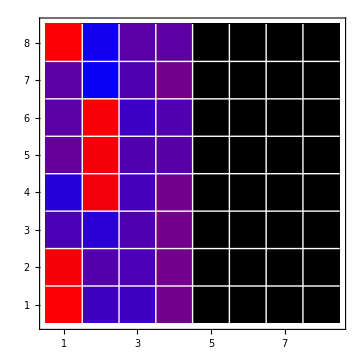
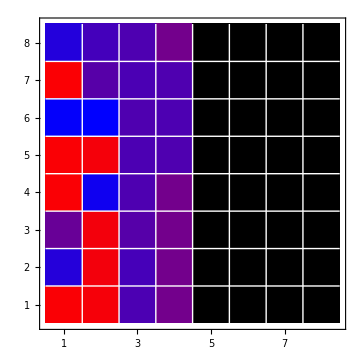
| Phase Behaviour of Surface Pulse | 
Sublattice A |  | Sublattice B
-Graphics- |  | -Graphics-

| Phase Behaviour of Surface Pulse | 
 |  | 
-Graphics- |  | -Graphics-

| Phase Behaviour of Surface Pulse | 
 |  | 
-Graphics- |  | -Graphics-

```mathematica
cells = Block[{reverseRange = Reverse[Range[8]]},
Table[{reverseRange[[i]],i},
{i,8}
]];
cells2 = Block[{range = Range[8]},Table[
{range[[i]],i},
{i,8}
]];

Grid[{{"",Text[Style["Phase Behaviour of Surface Pulse",FontSize->15]],""},{"Sublattice A","","Sublattice B"},{ArrayPlot[Transpose[coloredPulse][[;;,;;,1]],Mesh->{7,7},MeshStyle-> White,AspectRatio->1,Frame->True,FrameTicks->{cells,cells2},ImageSize->Medium]
,
BarLegend[{{RGBColor[1,0,0],RGBColor[0,0,1]},{0,2π}},LegendLayout->"Column",LegendLabel->"Phase of Node"]
,
ArrayPlot[Transpose[coloredPulse][[;;,;;,2]],Mesh->{7,7},MeshStyle-> White,AspectRatio->1,Frame->True,FrameTicks->{cells,cells2},ImageSize->Medium]}}]
```

```mathematica
Clear[arr]
func[x__]:=0.;
arr=Array[func,{Dimensions[sortedDataWithCorrds][[1]],Dimensions[sortedDataWithCorrds][[2]],128,Dimensions[dataOfNodes][[4]]}];
```

```mathematica
Dimensions[arr]
```

{4,8,128,2}

```mathematica
arr[[1,1,1]]//MatrixForm
```

(0.
0.)

```mathematica
Dimensions[sortedDataWithCorrds]
```

{4,8,2,2}

```mathematica
sortedDataWithCorrds[[1,1,All,2]]
```

{{1,1,1},{1,1,2}}

```mathematica
pos=Flatten[Table[{n*16+3+m},{n,0,7},{m,0,5}]];
rng=Range[Length[pos]];
```

```mathematica
pos
rng
```

{3,4,5,6,7,8,19,20,21,22,23,24,35,36,37,38,39,40,51,52,53,54,55,56,67,68,69,70,71,72,83,84,85,86,87,88,99,100,101,102,103,104,115,116,117,118,119,120}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48}

```mathematica
Reverse
```

Reverse

```mathematica
Do[
arr[[p,q,r[[2]],s]]=sortedDataWithCorrds[[p,q,r[[1]],s]],
{p,1,Dimensions[dataOfNodes][[1]]},{q,1,Dimensions[dataOfNodes][[2]]/50},{r,Transpose[{rng,pos}]},{s,1,2}]
```

Part::partw: Part 3 of {{{-0.000144671,-0.000219143,-0.000231962,-0.000219143,-0.000231962,-0.000219143,-0.000206934,-0.000269198,-0.000181907,-0.00024417,«19994»},{1,1,1}},{{0.000164815,0.000164815,0.000112929,0.000219753,0.0000579905,0.000112929,0.000112929,-0.0000488341,0.000112929,0.000164815,«19994»},{1,1,2}}} does not exist.

Part::partw: Part 4 of {{{-0.000144671,-0.000219143,-0.000231962,-0.000219143,-0.000231962,-0.000219143,-0.000206934,-0.000269198,-0.000181907,-0.00024417,«19994»},{1,1,1}},{{0.000164815,0.000164815,0.000112929,0.000219753,0.0000579905,0.000112929,0.000112929,-0.0000488341,0.000112929,0.000164815,«19994»},{1,1,2}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::partw: Part 9 of {<<20751848856 bytes>>} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

```mathematica
(*Weist dem Teil-Lattice von 48 Nodes dem kompletten Lattice mit 128 Nodes zu*)
```

```mathematica
times=sortedDataWithCorrds[[1,1,1,1,All,1]];
none={Transpose[{times,Table[0.,{Length[times]}]}],{-1,-1,-1}};
```

Part::partd: Part specification {{{{{-0.000144671, -0.000219143, -0.000231962, <<19999>>, <<12>>, -0.000181907}, {<<3>>}}, {<<2>>}}, <<7>>}, <<3>>}[[1,1,<<3>>,1]] is longer than depth of object.

Transpose::nmtx: The first two levels of {{{{{{-0.000144671, -0.000219143, <<10>>62, <<20000>>, -0.000181907}, {<<3>>}}, {<<2>>}}, <<7>>}, <<3>>}[[1,1,<<3>>,1]], {<<7>>}} cannot be transposed.

```mathematica
arr[[1,1,2,2]]//MatrixForm
```

0.

```mathematica
arr//Dimensions
```

{4,8,128,2}

```mathematica
arr[[1,1,5,2]]//MatrixForm
```

1⟦1,1,3,2⟧
 |  |  |  |

```mathematica
Do[
If[
Dimensions[arr[[p,q,r,1]]]=={},arr[[p,q,r]]=none
]
,{p,1,Dimensions[dataOfNodes][[1]]},{q,1,Dimensions[dataOfNodes][[2]]/50},{r,1,128}
]
```

Part::partw: Part 9 of {<<38790448536 bytes>>} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CorrectMean[data_]:=Block[{},mean = Mean[data[[;;,2]]];
dy = data[[;;,2]]-mean;
Transpose[{data[[;;,1]],dy}]];
```

```mathematica
arrMean[freq_,meas_]:= Table[CorrectMean[arr[[freq,meas,i,1]]],{i,1,128,1}];
```

```mathematica
arr//Dimensions
```

{4,8,128,2}

```mathematica
arrMeanTest = arrMean[1,2];
```

Transpose::nmtx: The first two levels of {Transpose[{{{{{-0.000144671, -0.000219143, <<20001>>, -0.000181907}, {<<3>>}}, {<<2>>}}, <<7>>}, <<3>>}[[1,1,<<3>>,1]]], <<1>>} cannot be transposed.

Part::partd: Part specification {-0.000252106,-0.000227079,-0.000202051,-0.000239287,-0.000277133,-0.000202051,-0.000227079,-0.000202051,-0.000239287,-0.000289342,«19994»}⟦1;;All,2⟧ is longer than depth of object.

Part::partd: Part specification {-0.000252106,-0.000227079,-0.000202051,-0.000239287,-0.000277133,-0.000202051,-0.000227079,-0.000202051,-0.000239287,-0.000289342,«19994»}⟦1;;All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Transpose[{{{{{-0.000144671, -0.000219143, <<20001>>, -0.000181907}, {<<3>>}}, {<<2>>}}, <<7>>}, <<3>>}[[1,1,<<3>>,1]]], <<1>>} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
GetMax[data_]:=Block[{},peaks=FindPeaks[data[[;;,2]],10,0,0.005];
If[Length[peaks]==0,{0,0},peaks[[1]]]]
```

```mathematica
arrGetMaxTest = Table[GetMax[arrMeanTest[[i]]],{i,1,128,1}];
```

FindPeaks::arg: The argument {1;;All,{-0.000252106,-0.000227079,-0.000202051,-0.000239287,-0.000277133,-0.000202051,-0.000227079,-0.000202051,-0.000239287,-0.000289342,«19994»}⟦1;;All,2⟧} at position 1 is not a consistent list of real values.

FindPeaks::arg: The argument {1;;All,{-0.000109877,-0.000161763,-0.000109877,-0.000109877,-0.000161763,-0.000161763,-0.000216701,-0.000161763,-0.000109877,-0.000109877,«19994»}⟦1;;All,2⟧} at position 1 is not a consistent list of real values.

FindPeaks::arg: The argument {1 ;; All, {{{{{-0.000144671, -0.000219143, <<20001>>, -0.000181907}, {<<3>>}}, {<<2>>}}, <<7>>}, <<3>>}[[1,2,3,1]][[<<2>>]]} at position 1 is not a consistent list of real values.

General::stop: Further output of FindPeaks::arg will be suppressed during this calculation.

```mathematica
arrGetMaxTest[[2,2]]
```

0

```mathematica
data=arrGetMaxTest;
```

```mathematica
maxTime = Max[data[[;;,1]]];
maxVoltage = Max[data[[;;,2]]];
emptyArray = RandomReal[0,{8,16}];
reshapedDataVoltages = ArrayReshape[data[[;;,2]],{8,16}];
reshapedDataTimes = ArrayReshape[data[[;;,1]],{8,16}];
Do[
emptyArray[[i,j]]={RGBColor[(reshapedDataTimes[[i,j]])/(maxTime),0,0,reshapedDataVoltages[[i,j]]/maxVoltage],reshapedDataVoltages[[i,j]]},
{i,8},{j,16}
]
totalTime = (0.000002485-(-0.0000025142))*10^6;
```

Part::partw: Part 3 of {{{-0.000252106,-0.000227079,-0.000202051,-0.000239287,-0.000277133,-0.000202051,-0.000227079,-0.000202051,-0.000239287,-0.000289342,«19994»},{1,2,1}},{{-0.000109877,-0.000161763,-0.000109877,-0.000109877,-0.000161763,-0.000161763,-0.000216701,-0.000161763,-0.000109877,-0.000109877,«19994»},{1,2,2}}} does not exist.

Part::partd: Part specification {{{{{-0.000144671, -0.000219143, -<<9>>62, <<20000>>, -0.000181907}, {<<3>>}}, {<<2>>}}, <<7>>}, <<3>>}[[1,2,3,1]][[<<2>>]] is longer than depth of object.

Part::partw: Part 4 of {{{-0.000252106,-0.000227079,-0.000202051,-0.000239287,-0.000277133,-0.000202051,-0.000227079,-0.000202051,-0.000239287,-0.000289342,«19994»},{1,2,1}},{{-0.000109877,-0.000161763,-0.000109877,-0.000109877,-0.000161763,-0.000161763,-0.000216701,-0.000161763,-0.000109877,-0.000109877,«19994»},{1,2,2}}} does not exist.

Part::partd: Part specification {{{{{-0.000144671, -0.000219143, -<<9>>62, <<20000>>, -0.000181907}, {<<3>>}}, {<<2>>}}, <<7>>}, <<3>>}[[1,2,4,1]][[<<2>>]] is longer than depth of object.

Part::partw: Part 5 of {{{-0.000252106,-0.000227079,-0.000202051,-0.000239287,-0.000277133,-0.000202051,-0.000227079,-0.000202051,-0.000239287,-0.000289342,«19994»},{1,2,1}},{{-0.000109877,-0.000161763,-0.000109877,-0.000109877,-0.000161763,-0.000161763,-0.000216701,-0.000161763,-0.000109877,-0.000109877,«19994»},{1,2,2}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification {{{{{-0.000144671, -0.000219143, -<<9>>62, <<20000>>, -0.000181907}, {<<3>>}}, {<<2>>}}, <<7>>}, <<3>>}[[1,2,5,1]][[<<2>>]] is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
cells = Block[{reverseRange = Reverse[Range[8]]},
Table[{reverseRange[[i]],i},
{i,8}
]];
cells2 = Block[{range = Range[2,16,2]-0.5},Table[
{range[[i]],i},
{i,8}
]];

size = 10;
emptyGradient = RandomReal[0,{size,size}];
Do[
emptyGradient[[i,j]]=RGBColor[j/size,0,0,i/size],
{i,size},{j,size}
]
```

```mathematica
{arr[[1,1,3+5*16,1]][[1,1]],arr[[1,1,3+5*16,1]][[1,2]]}
```

{{1},{1}}
 |  |  |  |

```mathematica
cellConvention = Flatten[Table[i,{i,1,16}]];

sublatticeCorrection1 = If[cellInputNode1[[3]]=="A",-1,0];
translatedCellPositionX1 =  cellConvention[[2*cellInputNode1[[1]]+sublatticeCorrection1]];

sublatticeCorrection2 = If[cellInputNode2[[3]]=="A",-1,0];
translatedCellPositionX2 =  cellConvention[[2*cellInputNode2[[1]]+sublatticeCorrection2]];
```

```mathematica
pulseOverTime[frequencySelected_,measurmentNumber_]:= ParallelTable[{arr[[frequencySelected,measurmentNumber,xcoord+ycoord*16,1]][[i,1]],arr[[frequencySelected,measurmentNumber,xcoord+ycoord*16,1]][[i,2]]},{xcoord,1,16},{ycoord,0,7},{i,1,Dimensions[tbl][[3]]}]
```

```mathematica
pulseOverTimeTable = pulseOverTime[1,1];
```

LinkObject::linkw: Unable to write data to closed link ….

KernelObject::rdead: Subkernel connected through … appears dead.

```mathematica
pulseOverTimeTable2 = pulseOverTime[1,3];
```

```mathematica
pulseOverTimePlotsArray=ParallelTable[{ListLinePlot[pulseOverTimeTable[[j,i]],ImageSize->Medium,Frame->True,FrameLabel->{"Time in [μs]","Voltage in [mV]"},PlotRange->All,PlotLabel->ToString[If[i==cellInputNode1[[2]],If[j==translatedCellPositionX1,"First Input Node: ",""],""]]<>ToString[If[i==cellInputNode2[[2]],If[j==translatedCellPositionX2,"Second Input Node: ",""],""]]<>"("<>ToString[cellInputNode1[[1]]]<>","<>ToString[i]<>","<>ToString[cellInputNode1[[3]]]<>")"]},{j,1,16},{i,1,8}];
```

```mathematica
pulseOverTimePlotsColumn=Reverse[pulseOverTimePlotsArray[[translatedCellPositionX1]]];
pulseOverTimeTable[[1,1]][[1]]
```

{-0.569281,0.}

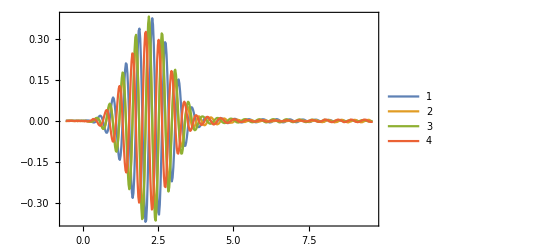

```mathematica
ListLinePlot[{pulseOverTimeTable[[6,3]],pulseOverTimeTable[[6,4]],pulseOverTimeTable2[[6,3]],pulseOverTimeTable2[[6,4]]},PlotLegends->Automatic,Frame->True,PlotRange->All]
```

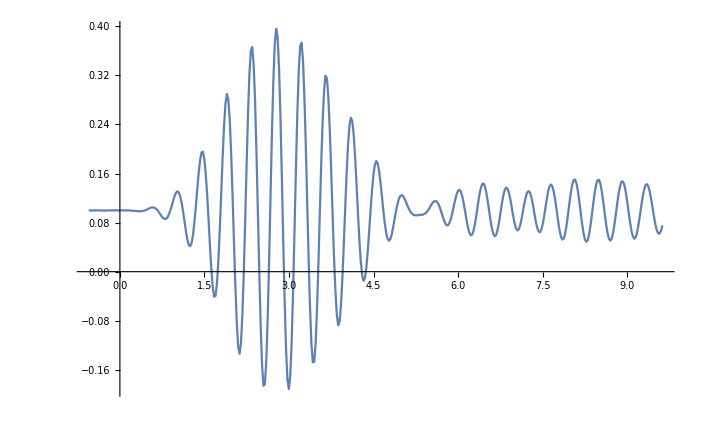

```mathematica
ListLinePlot[ParallelTable[pulseOverTimeTable[[6,i]]+ConstantArray[{0,0.02}*i,Length[pulseOverTimeTable[[6,i]]]],{i,{5}}],PlotRange->All]
```

```mathematica
π/2 /(2.286)
```

0.687138

```mathematica
Solve[x*0.1 == π/2,x]
```

{{x→15.708}}

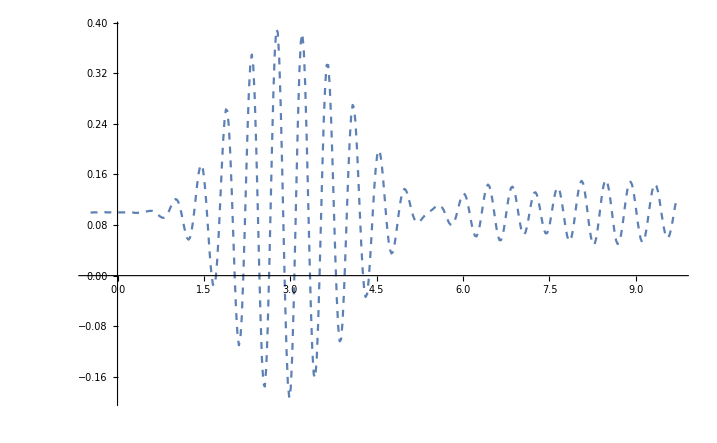

```mathematica
ListLinePlot[ParallelTable[pulseOverTimeTable2[[6,i]]+ConstantArray[{0.1,0.02*i},Length[pulseOverTimeTable2[[6,i]]]],{i,{5}}],PlotRange->All,PlotStyle->Dashed]
```

```mathematica
overlapDifferential = ParallelTable[Show[ListLinePlot[pulseOverTimeTable[[6,ynode]],PlotRange->All],ListLinePlot[pulseOverTimeTable2[[6,ynode]]+ConstantArray[{0.1,0},Length[pulseOverTimeTable2[[6,1]]]],PlotRange->All,PlotStyle->Dashed]],{ynode,1,8}];
```

```mathematica
Manipulate[overlapDifferential[[ynode]],{ynode,1,8,1}]
```

Part::partd: Part specification overlapDifferential⟦4⟧ is longer than depth of object.

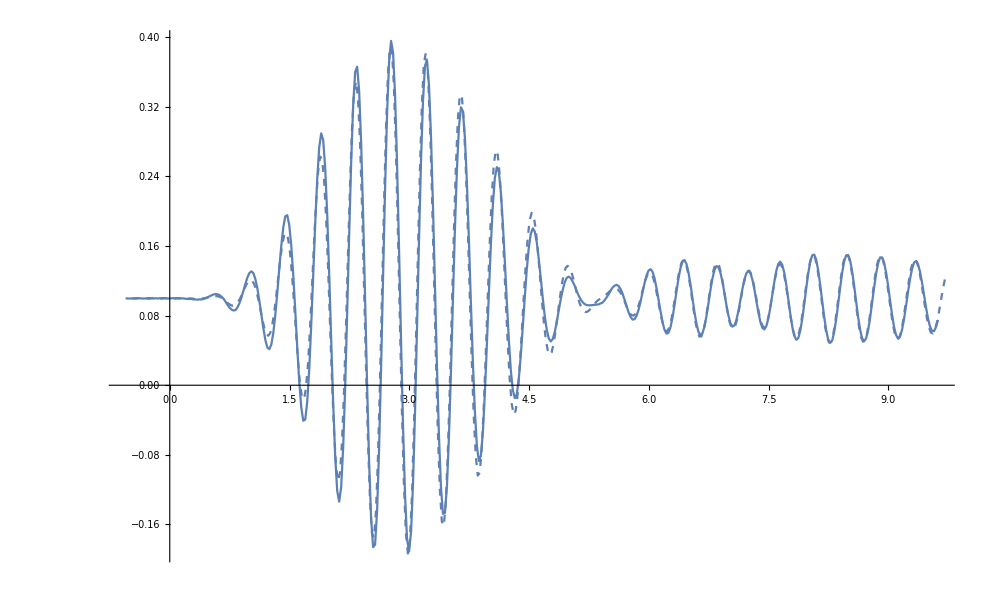

```mathematica
Show[%230,%231]
```

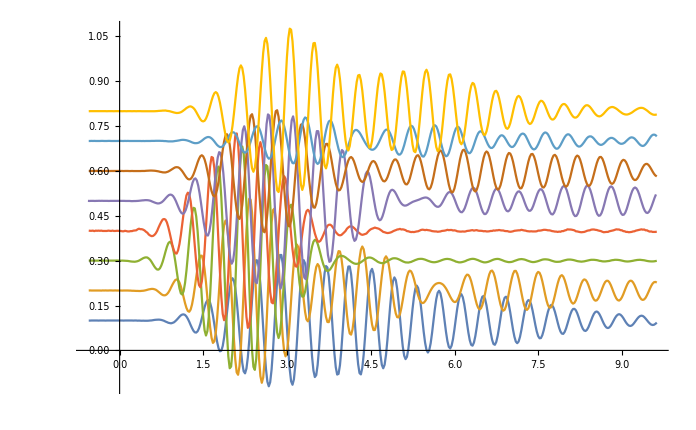

```mathematica
ListLinePlot[ParallelTable[pulseOverTimeTable2[[6,i]]+ConstantArray[{0,0.1}*i,Length[pulseOverTimeTable2[[6,i]]]],{i,1,8}]]
```

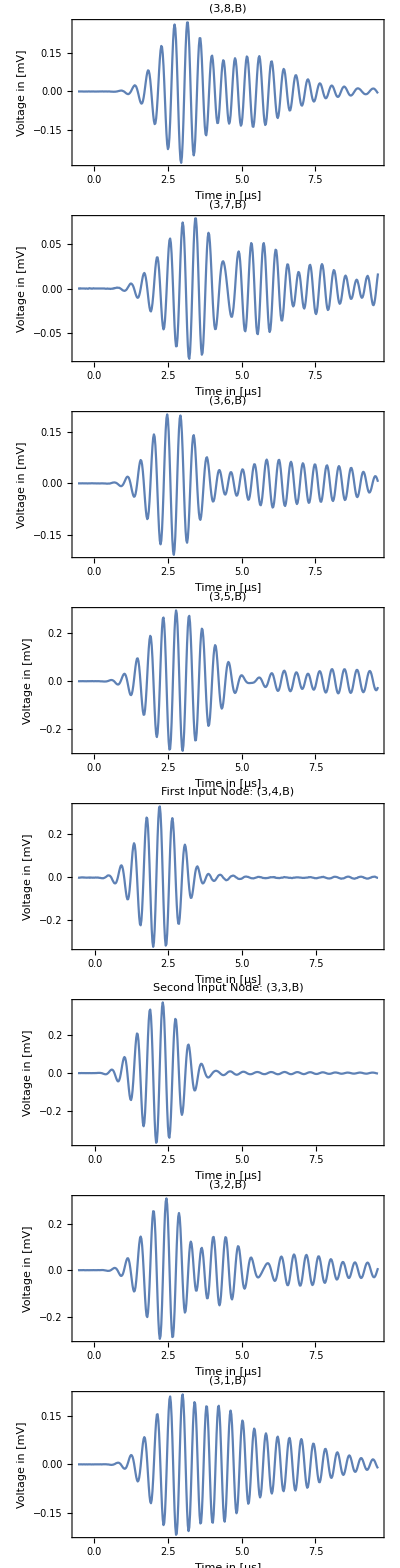

```mathematica
Grid[pulseOverTimePlotsColumn]
```

```mathematica
dataOfNodes//Dimensions;
controlNodes =dataOfNodes[[1,{30,32}]];
```

```mathematica
π/2 /(2.286)/(dataOfNodes[[1,1,2,1]]-dataOfNodes[[1,1,1,1]])
```

27.4855

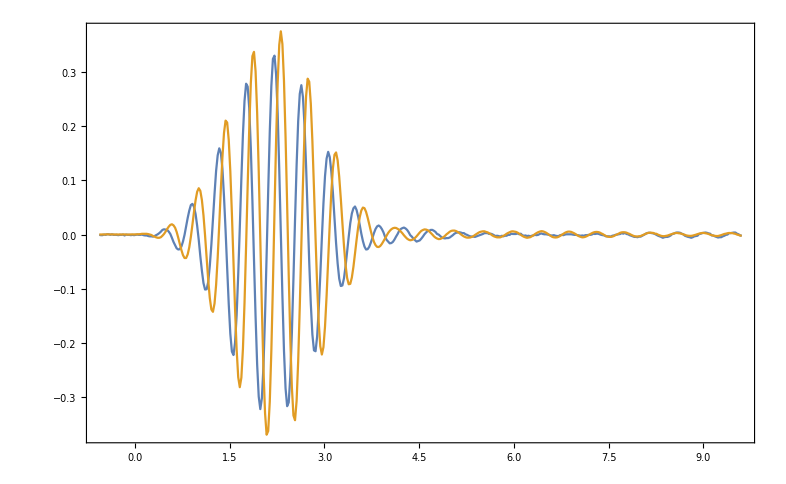

```mathematica
ListLinePlot[controlNodes[[;;]],Frame->True,PlotRange->All]
```

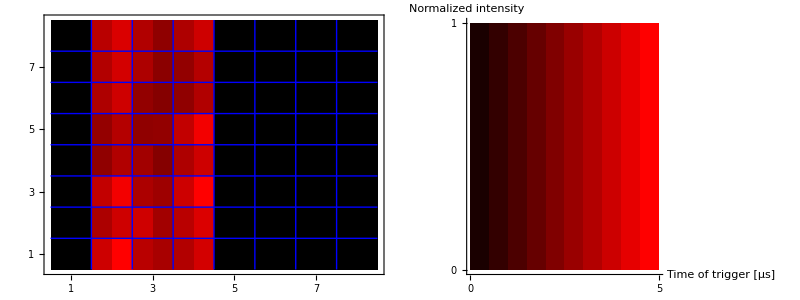

```mathematica
Grid[{{ArrayPlot[emptyArray[[;;,;;,1]],Mesh->{7,7},MeshStyle-> Blue,AspectRatio->1,Frame->True,FrameTicks->{cells,cells2},ImageSize->Medium],

ArrayPlot[Reverse[emptyGradient],Ticks->{{{0,0},{size,5}},{{0,0},{size,1}}},Frame->False,Axes->True,AxesLabel->{"Time of trigger [μs]","Normalized intensity"},ImageSize->Medium]
}}]
```

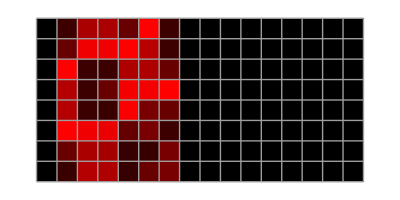

```mathematica
(*------------------*)
```

```mathematica
(*
inputNodes=If[StringSplit[path,"\\"][[-1]]=="4_4_A",{{4,4,"A"},{4,3,"A"}},{{4,2,"A"},{4,1,"A"}}];



dataWithCorrds=Map[Transpose[{#,correspondingNodeCoords}]&,arr,2];


boardA=Map[Partition[#[[1;;64]],8]&,sortedDataWithCorrds];
boardB=Map[Partition[#[[65;;All]],8]&,sortedDataWithCorrds];
max=Map[Max[#[[All,1,All,2]]]&,sortedDataWithCorrds];
riffledboards=Table[Riffle[boardA[[q]],boardB[[q]]],{q,1,Length[boardA]}];
*)
```

```mathematica
(*wholeThingyTest=Map[Flatten[Riffle[#[[1;;64]],#[[65;;All]]][[All,1,All,2]]]&,sortedDataWithCorrds];*)
maxWholeThingy=Table[Max[Abs[arr[[p,q,All,1]][[All,All,2]]]],{p,1,8},{q,1,6}];
```

```mathematica
(*ColorData["CandyColors"][0.5(Tan[0.9*Pi/2*x/maxWholeThingy[[1]]]/Tan[0.9*Pi/2]+1)]*)

col[x_,indMeas_,indFrequ_]:=ColorData["CandyColors"][0.5(x/maxWholeThingy[[indMeas,indFrequ]]+1)];
inputNodes={3,1}
```

{3,1}

```mathematica
colData=Table[col[arr[[meas,frequ,pos128,1,step,2]],meas,frequ],{meas,1,Dimensions[arr][[1]]},{frequ,1,Dimensions[arr][[2]]},{pos128,1,128},{step,1,407}];
```

```mathematica
boardsColData=ArrayReshape[colData,{8,6,8,16,407}];
```

```mathematica
Manipulate[MatrixPlot[boardsColData[[measurement,frequency,All,All,timestep]],PlotLabel->"Dynamic measurement @ 2.4 MHz, input nodes: "<>ToString[inputNodes[[1]]]<>", "<>ToString[inputNodes[[2]]]<>"\nphase: CH1 to CH2:  "<>ToString[If[measurement==1,-Pi,Pi]]<>" / 2"],{frequency,1,6},{measurement,1,Dimensions[colData][[1]],1},{timestep,1,407,1}]
```

Part::partd: Part specification boardsColData⟦1,1,All,All,1⟧ is longer than depth of object.

Part::partd: Part specification inputNodes⟦1⟧ is longer than depth of object.

Part::partd: Part specification inputNodes⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

MatrixPlot::mat0: Argument boardsColData⟦1,1,All,All,1⟧ at position 1 is not a matrix.

Part::partd: Part specification boardsColData⟦1,1,All,All,1⟧ is longer than depth of object.

Part::partd: Part specification inputNodes⟦1⟧ is longer than depth of object.

Part::partd: Part specification inputNodes⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

MatrixPlot::mat0: Argument boardsColData⟦1,1,All,All,1⟧ at position 1 is not a matrix.

Part::partd: Part specification boardsColData⟦1,1,All,All,1⟧ is longer than depth of object.

Part::partd: Part specification inputNodes⟦1⟧ is longer than depth of object.

Part::partd: Part specification inputNodes⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

MatrixPlot::mat0: Argument boardsColData⟦1,1,All,All,1⟧ at position 1 is not a matrix.

Part::partd: Part specification boardsColData⟦1,1,All,All,1⟧ is longer than depth of object.

Part::partd: Part specification inputNodes⟦1⟧ is longer than depth of object.

Part::partd: Part specification inputNodes⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

MatrixPlot::mat0: Argument boardsColData⟦1,1,All,All,1⟧ at position 1 is not a matrix.

Part::partd: Part specification boardsColData⟦1,1,All,All,1⟧ is longer than depth of object.

Part::partd: Part specification inputNodes⟦1⟧ is longer than depth of object.

Part::partd: Part specification inputNodes⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

MatrixPlot::mat0: Argument boardsColData⟦1,1,All,All,1⟧ at position 1 is not a matrix.